94/(94+s)

752

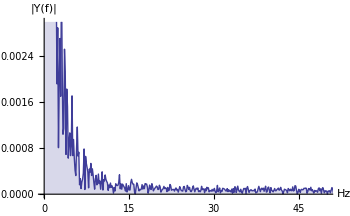

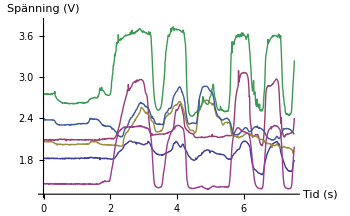

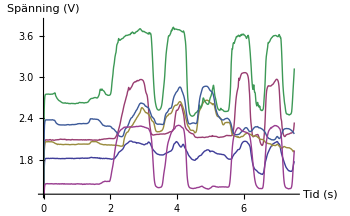

~/kandidat/Slutrapport/img/filter/flex_fourier.pdf

~/kandidat/Slutrapport/img/filter/flex_raw.pdf

~/kandidat/Slutrapport/img/filter/flex_filtered.pdf

```mathematica
ClearAll["Global`*"]

SetOptions[{Plot,ParametricPlot, ListLinePlot, ListPlot},BaseStyle->{FontFamily->"Latin Modern Roman", FontSize->11}];
breakfreq = IntegerPart[15*2*Pi];
sr = 100;



ButterworthFilterModel[{1, breakfreq}, s]
tf = ToDiscreteTimeModel[%, 1/sr, z];
(*BodePlot[tf]*)

(*unsigned long ret=(breakfreq*(((unsigned long)s->xp)+((unsigned long)x))-s->yp*(breakfreq-2*hz))/(breakfreq+2*hz);*)

data = Transpose[Import["~/kandikod/measure/samples2.tsv"]] * 5/1024;
samples = Length[data[[1]]]
index = PlotLegends-> (Style [#, FontSize -> 10, FontFamily->"Latin Modern Roman"]& /@ {"Tumme 0", "Tumme 1", "Pekfinger 0", "Pekfinger 1", "Långfinger 0", "Långfinger 1"});
range = {PlotRange->{Full, {1.3, 3.8}}, DataRange->{0, (samples-1)/sr}, AxesLabel->{"Tid (s)", "Spänning (V)"}};

totdft = Total[Fourier /@ data];
(*totdft = Fourier[data[[1]]];*)
p0 = ListPlot[
2*Abs[totdft]/samples
, DataRange->{0,  sr}
, PlotRange->{{0, sr/2}, {0, 0.003}}
, ImageSize->350
, Joined->True
,AxesLabel->{"Hz", "|Y(f)|"}
, Filling->Axis
]


filtered = RecurrenceFilter[tf, #] & /@ data;
unitResponse = RecurrenceFilter[tf, Array[UnitStep,  sr]];
p1 = ListLinePlot[data, range, ImageSize->350]
p2 = ListLinePlot[filtered,  range, ImageSize->350]

(*ListLinePlot[{data[[4]], filtered[[4]]}, PlotRange -> {{3,4},{1, 1023}}, DataRange->{0, (samples-1)/sr}, AxesLabel->{"Tid (s)", "f(t)"}]
*)
(*p1 =  ListLinePlot[unitResponse, ImageSize->418, DataRange->{0, 1000},AxesOrigin->{0,0}, AxesLabel->{"Tid (ms)"}, PlotRange->{{0, 100},Full}]*)

Export["~/kandidat/Slutrapport/img/filter/flex_fourier.pdf", p0]
Export["~/kandidat/Slutrapport/img/filter/flex_raw.pdf", p1]
Export["~/kandidat/Slutrapport/img/filter/flex_filtered.pdf", p2]
```

```mathematica
First[%1683]
```